```mathematica
f[n_]= n^2(Log[n-Sqrt[n^2-2]]+Log[n])
```

n^2 (Log[n]+Log[n-√(-2+n^2)])

```mathematica
Limit[f[n],n-> Infinity]
```

1/2

```mathematica
a[n_]= If[n==1, 1, 1+(5/a[n-1])]
```

If[n==1,1,1+5/a[n-1]]

```mathematica
a[10]
```

17621/6191

```mathematica
N[%]
```

2.84623

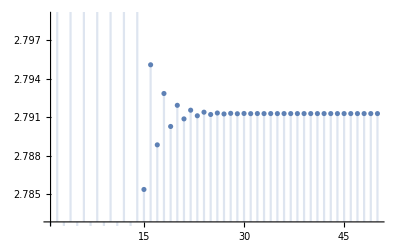

```mathematica
DiscretePlot[a[n],{n,1,50}]
```

```mathematica
Table[a[n],{n,1,50}]
```

{1,6,11/6,41/11,96/41,301/96,781/301,2286/781,6191/2286,17621/6191,48576/17621,136681/48576,379561/136681,1062966/379561,2960771/1062966,8275601/2960771,23079456/8275601,64457461/23079456,179854741/64457461,502142046/179854741,1401415751/502142046,3912125981/1401415751,10919204736/3912125981,30479834641/10919204736,85075858321/30479834641,237475031526/85075858321,662854323131/237475031526,1850229480761/662854323131,5164501096416/1850229480761,14415648500221/5164501096416,40238153982301/14415648500221,112316396483406/40238153982301,313507166394911/112316396483406,875089148811941/313507166394911,2442624980786496/875089148811941,6818070724846201/2442624980786496,19031195628778681/6818070724846201,53121549253009686/19031195628778681,148277527396903091/53121549253009686,413885273661951521/148277527396903091,1155272910646466976/413885273661951521,3224699278956224581/1155272910646466976,9001063832188559461/3224699278956224581,25124560226969682366/9001063832188559461,70129879387912479671/25124560226969682366,195752680522760891501/70129879387912479671,546402077462323289856/195752680522760891501,1525165480076127747361/546402077462323289856,4257175867387744196641/1525165480076127747361,11883003267768382933446/4257175867387744196641}

```mathematica
N[%]
```

{1.,6.,1.83333,3.72727,2.34146,3.13542,2.59468,2.92702,2.70822,2.84623,2.75671,2.81376,2.77698,2.80051,2.78539,2.79508,2.78886,2.79285,2.79029,2.79193,2.79088,2.79155,2.79112,2.7914,2.79122,2.79133,2.79126,2.79131,2.79128,2.7913,2.79128,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129,2.79129}

```mathematica
a[n_]= If[n==1, 1, 1+(5/a[n-1])]
```

```mathematica
Solve[x ==1+5/(x),x]
```

{{x→1/2 (1-√21)},{x→1/2 (1+√21)}}

RSolve::argm: RSolve called with 2 arguments; 3 or more arguments are expected.

```mathematica
Biseccio[f_,{a_,b_,M_}]:=Module[{an,bn,xn},
an=a;
bn=b;
For[i=1,i≤M,i++,
xn=N[(an+bn)/2,20];
If[f[xn]==0,Break[],
If[f[an]*f[xn]<0, bn=xn,
If[f[xn]*f[bn]<0,an=xn]
]
]
];
N[xn,20]
]
```

```mathematica
g[x_]=x^7-123
```

-123+x^7

```mathematica
Solve[g[x]==0,x]
```

{{x→-(-123)^(1/7)},{x→123^(1/7)},{x→(-1)^(2/7) 123^(1/7)},{x→-(-1)^(3/7) 123^(1/7)},{x→(-1)^(4/7) 123^(1/7)},{x→-(-1)^(5/7) 123^(1/7)},{x→(-1)^(6/7) 123^(1/7)}}

```mathematica
N[%]
```

{{x→-1.79171-0.862842 ⅈ},{x→1.98865},{x→1.2399+1.55479 ⅈ},{x→-0.442516-1.93879 ⅈ},{x→-0.442516+1.93879 ⅈ},{x→1.2399-1.55479 ⅈ},{x→-1.79171+0.862842 ⅈ}}

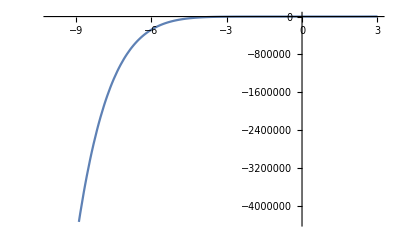

```mathematica
Plot[g[x],{x,-10,3}]
```

```mathematica
Reduce[(10^-11 <(3-1)/2^n),n,Reals]
```

n<(12 Log[2]+11 Log[5])/Log[2]

```mathematica
N[%]
```

n<37.5412

```mathematica
Biseccio[g,1,3,38]
```

```mathematica
Biseccio[g,{1,3,38}]
```

1.9886477952750283293

```mathematica
1.9886477952750283293426036834716796875`20.
```

1.9886477952750283293

```mathematica
1.9886477952750283293426036834716796875`20.
```

1.9886477952750283293

```mathematica
Clear[n]
Clear[a]
```

```mathematica
a[0]
```

a[0]

```mathematica
∑_(n=1)^Infinity ((2n^2+5)(-1)^(n+1))/n^4
```

```mathematica
1/144 π^2 (24+7 π^2)
N[%,20]
```

1/144 π^2 (24+7 π^2)

6.3800982143344560244

```mathematica
Reduce[10^-6<(2(n+1)^2+5)/(n+1)^4,n,Reals]
```

Root[-6999999-3999996 #1-1999994 #1^2+4 #1^3+#1^4&,1]<n<-1||-1<n<Root[-6999999-3999996 #1-1999994 #1^2+4 #1^3+#1^4&,2]

```mathematica
N[%]
```

-1415.21<n<-1.||-1.<n<1413.21

```mathematica
∑_(n=1)^1412 ((2n^2+5)(-1)^(n+1))/n^4
```

145049292440575435074275496201831955253363037620198470004858297154971060696345650561206448599024324752023089856541790614060138748628571878463159117579161540537534389388390153741269647458379623383737220418377084576974166286654632520071950728598223486893090024805631431551119524550884490159800572703242384016594502976871651541387372323548558346372623797544261534052697693070143305838207145916439343734334705899567196709105387181931427896279021348682279528578402417217533058247601612242503805603404415538562309280151693190996688702440698914967124965183465116553244225831412157975236388418040426395508068003824387206695054432181711860130490659870784070323722904194093716981805230270027702500221475999346127952543276223738797299310496907308595115064917634399064558898570384910835684310785690168688487895061838970956124233166907702802702942788347452894581646297166100043437041555337812534066615972599021071041181156599447535519616283913894229693305719252750745664413892496194508674144960098269869623228555568543032941357885697386643348260672511880052098097629494810710827364748346652342771134909947085777357006620198468929233467199787848229222768729550919388170618547858296518978382007172819342614556575745082512877226162411605348915562489161082796799298386128656211898189604303573616250143232053386286097722050325698866670916777647937536175650517097038313657434441595683325095001220172352538407519437295378732962422598540899910755262786185199667808749475637589727643503986303687275032726341868952964748647117115295468236580699948404197698675662492813141443565657859511372041339927133450200757336570620295893613196018184659119026814474473340776280942650033350009945736969333928298997929037164495475925835010486109310816137842894954790657163757407712534964083051218594894434759835883363549982301706986671244148620044722096517588070358904062712781949907163499317401574928161925583756744907165937445300562757699372410100704072516010807501922983905241910121548334872103445552645614337104584490367847669862546642897607542003285411832537305882214081414735757978294152689868005829514464253325137085949568308346906935654512300147859481878951689481924013046219380578674086167620077146963559068260876556906498441800977289482440634968504780255445883829919478748111455401326253415819865617005305833600361674892082730177111741566149355537553796531373680478450717511166262087502281559811290086406553904258011468906833195998451377818251963/22734650616728518307398157759731456137726034406273640911755952222486698561675364713176451193682457437569136237513307698785534142815462797656883640893978176416120958960448618668593569293681281965394710774059397885493444765825232256143425923747214190998963942917677199778867151108964724951138163512698977284079072638146831681550476564866994054666407283556063342046333981043699028900414254094339740049826440666053749158148335146847711981764155815336856536193119019750442111437880890835428192472266044400606038803392801228689968563138500334277997421296465249706128630658215484232977919204758562924330306435179622605337413511001066250014334780220966552372644729128292861262525978220233347638093833288824126354491682801237000114865531869130560391086205383945157652689342283037422915716668929541796587914941405482895237555012122870018018069195905266277645718068491711020504360283439208810088767794097198308764659106553466583611705492411904399563323553825747838532856334155547940877496785874887472260019651789498043148813989920818866825810503567141221507934225036332468278312152371788317495562720012941194850582606075888312677254456338718886357875940392957484204010633978886780509344050435018881555821633734064731010286792699667559350399061621924753778211398667155057037547769677990493438573763944559774848270131008869362992611830420543750030557045417852551272370356683039698134758044262914813869621524665929394658341935150969352241186650514766509842380250775197675602291970683419175006457518562548668305762091574088732381199429666066811842276288863393417081387354523491958814222099224417546249887084733649375796314095442329156481584384547585723169283029883329508601731841968626940694878715650600930144556461473198043546527496710637761481816109534361698474816325003759722275184804480738670808023109089714444363511728773832185642365295503613269410053404803279218080403405614051491701609219580102528163206357084687085898198384136036085048714623255212175780577798787988542135555330454473673993341179954294590475343733910713702154981708171453382008177956292658401621246183652964991919002158511278743388896236255089896488598612673039880888201654598148507273476440343313009035581084712716962098574479903491052519360912281072997929564118291408833822354480179126540194606284451134033351154546881119209667503931500136834742202437268858759935839894931674966255640398843624852612819320019535124917751851555399286873548390400000000000000

```mathematica
N[%111,20]
```

6.3800977131201390389

```mathematica
Clear[a]
```

```mathematica
Clear[n]
```

If::argb: If called with 5 arguments; between 2 and 4 arguments are expected.

If[n==0,-3,n==1,-2,9 a[n-1]-14 a[n-2]+5 n]

```mathematica
Clear[a]
```

```mathematica
Clear[n]
```

```mathematica
RSolve[{a[n+2]==9a[n+1]-14a[n]+5n,a[0]==-3,a[1]==-2},a[n],n]
```

{{a[n]→1/180 (175-27 2^(5+n)+149 7^n+150 n)}}

```mathematica
Limit[1/180 (175-27 2^(5+n)+149 7^n+150 n),n->Infinity]
```

∞

```mathematica
Reduce[1/180 (175-27 2^(5+1)+149 7^1+150 n)/d^1<0,d]
```

(n<17/5&&d>0)||(n>17/5&&d<0)

```mathematica
N[%]
```

(n<3.4&&d>0.)||(n>3.4&&d<0.)

RSolve::dsfun: True cannot be used as a function.

$Aborted